```mathematica
(*Código utilizado para obtener las secciones de Poincaré del sistema dada una energía y un k. Basado en el código fuente de Mathematica https://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/poincare-sections.html. Adaptado al problema por Gustavo Ardila y Cristian Tibambre*)
```

```mathematica
(* lo hacemos con k=0.0*)
```

```mathematica
(*Constantes y parametro de control*)
k0=0;
m=5;
g=9.8;
```

```mathematica
(*Ecuaciones diferenciales*)
ecuaciones={p'[s]==-k0*(Sin[h[s]]-Sin[j[s]])*Cos[h[s]]-m*g*Sin[h[s]], h'[s]==p[s]/m, q'[s]==k0*(Sin[h[s]]-Sin[j[s]])*Cos[j[s]]-m*g*Sin[j[s]], j'[s]==q[s]/m};
```

```mathematica
(*Guarda la sección dada la solucion obtenida usando NDSolve y si esta cumple ciertas condiciones.*)
```

```mathematica
secciones[{a0_,b0_,c0_,d0_}]:=Reap[NDSolve[{ecuaciones, h[0]==a0, j[0]==b0, p[0]==c0, q[0]==d0, WhenEvent[q[s]==0, Sow[{h[s],p[s]}]]},{h[s],j[s], p[s], q[s]},{s,0,1000}, MaxSteps->Infinity]][[-1,1]];
```

```mathematica
(*Calcula la sección*)
info= Map[secciones, bunch]
```

{{{5.86282,7.25907},{6.70848,7.02033},{5.93235,7.69767},{6.66595,9.17952},379,{6.69773,6.36072},{5.61217,0.590815},{7.01135,-0.281158}},261,{1}}
 |  |  |  |

```mathematica
Length[info]
```

281

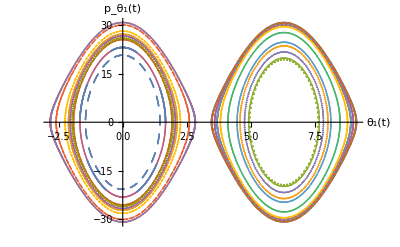

```mathematica
ListPlot[{info[[3]],info[[4]],info[[7]],info[[10]],info[[11]],info[[14]],info[[15]],info[[16]],info[[18]],info[[24]],info[[26]],info[[27]],info[[34]],info[[35]],info[[36]],info[[40]],info[[46]],info[[52]],info[[53]],info[[55]],info[[58]],info[[60]],info[[61]],info[[65]]}, ImageSize->Full, AxesLabel->{Style["θ_1(t)", Bold,20,Black], Style["p_θ_1(t)", Bold,20,Black]}]
```